```mathematica
(*Malthus Model*)
(*Initialize Kernel*)
```

```mathematica
ClearAll;
(*Solve, analytically, the Malthus differential equation for exponential population growth*)
```

```mathematica
DSolve[{n'[t]==r*(n[t]),n[0]==N0},n[t],t]
```

{{n[t]→ⅇ^(r t) N0}}

```mathematica
(*Convert solution to function*)
```

```mathematica
n[t_]:=N0*ⅇ^(r t)
```

```mathematica
(* Find Real Zeros*)
realzero=n[t]/. Solve[n'[x]==0,Reals];
```

```mathematica
(*Phase Portrait (in red, unstable fixed points, in black stable fixed points)*)
```

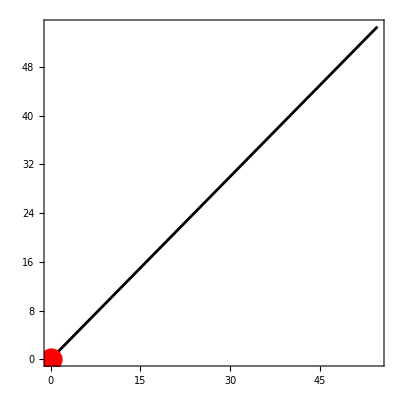

```mathematica
Show[ParametricPlot[{n[t]/.{r->1,N0->1},n'[t]/.{r->1,N0->1}},{t,0,4},PlotStyle->Black], Epilog->{PointSize[0.04],Red,Tooltip[#,#[[1]]]&@Point[{realzero[[1]],0}]},AspectRatio->1,Frame->True,FrameLabel->(Style[#,14]&/@{"",""})]
```

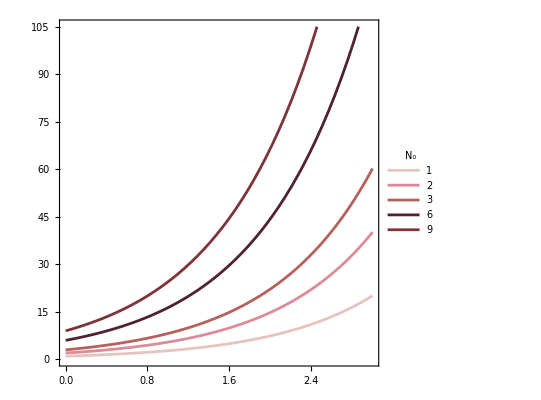

```mathematica
(*Plot n(t) versus t for r=1 and N0 ranging 1 to 4*)Plot[Evaluate@Table[n[t]/.r->1,{N0,{1,2,3,6,9}}],{t,0,3},Frame->True,PlotLegends->LineLegend[Table[N0,{N0,{1,2,3,6,9}}],LegendLabel->],AspectRatio->1,FrameLabel-> {"",""},PlotStyle->ColorData[62,"ColorList"]]
```